# Stepping probability

## Stepwise progress of molecular motors

#### G. Woehlke, 2024 ff

## Introduction and initialization

A large number of independent motor proteins that have the probability p to step forwards in the interval Δt will be distributed according to a binomial distribution, in Mathematica syntax BinomialDistribution[n,p]. In this calculation example, the number of trials (or time slots) is n = 40, the stepping probability per time interval is p = 0.05. Then, this function returns the probability of finding motors that have travelled exactly two steps:

```mathematica
PDF[BinomialDistribution[40,0.05],2] (* vary values BinomialDistribution[n,p] ! *)
```

0.277672

```mathematica
binD[n_,p_]:=BinomialDistribution[n,p]
```

From a theoretical perspective, each stepping probability produces a characteristic mean travel distance whose variance spreads linearly with the distance. Play with the parameters below:

The probability density function PDF[...,k] displays the probabilities of finding motors that have travelled k steps after 40 time intervals.

```mathematica
Manipulate[DiscretePlot[PDF[BinomialDistribution[40,p(*0.5*)],k]//Evaluate,{k,50},PlotRange->All,PlotStyle->color,PlotMarkers->Automatic, LabelStyle->Directive[FontFamily->Arial,fs],AxesLabel->{"Travel distance/steps", "Probability"},ImageSize->is],
{color,{Blue,RGBColor[0.5,0.5,0.85],Orange,Gray,Red,Darker[Green]}},
{{fs,21,"font size"},{14,18,21,24,28}},
(*{{thn,0.005,"line thickness"},0.001,0.025},*)
{{is,720,"image size"},{450,650,720,950,1080}},
(*{{n,40,"number of time slots"},10.,100.,Appearance->"Open"},*)
{{p,0.5,"stepping probability"},0.001,1.,Appearance->"Open"}]
```

## Simulation with random data

```mathematica
CellPrint[TextCell["Set Stepping Probabilities",CellTags->"p","Subsection"]]
```

### Set Stepping Probabilities

```mathematica
p=0.5;
```

We can use the probability distribution to generate sample data of 100 molecular motors:

```mathematica
data=RandomVariate[BinomialDistribution[40,p],100]
```

{17,15,15,23,16,20,16,19,23,18,22,15,23,21,16,20,22,15,22,20,17,18,23,19,21,21,16,19,16,16,23,17,20,25,24,28,22,23,27,21,24,20,14,25,23,19,19,18,20,23,23,23,25,16,23,22,19,16,16,26,24,21,15,20,18,25,18,22,20,20,19,19,18,24,17,18,22,22,25,19,20,19,21,23,20,21,25,19,21,21,17,15,18,25,18,23,21,19,18,15}

For a meaning of the following expression, see below:

```mathematica
Dynamic[2. Mean[data]/Variance[data]]
```

We find that the simulated data resembles a “Gaussian bell curve”, formally a normal distribution (please update!)

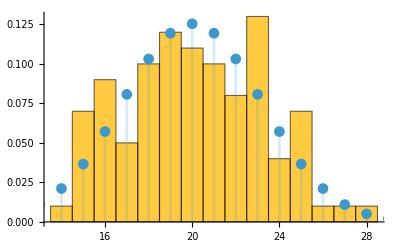

```mathematica
Show[Histogram[data,20,"ProbabilityDensity"],
DiscretePlot[PDF[BinomialDistribution[40,p],k]//Evaluate,{k,50},PlotRange->All,PlotMarkers->Automatic]]
```

```mathematica
Button["Enter new probability",NotebookLocate[{"MathCode_20_SteppingProbability.nb","p"}],Background->LightYellow]
```

Enter new probability

Theory:

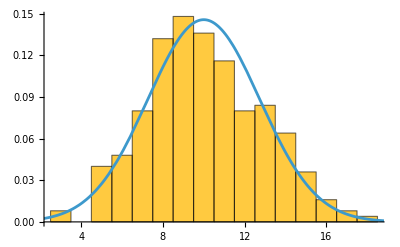

```mathematica
Show[
Histogram[RandomVariate[BinomialDistribution[40,0.25],250],35,"ProbabilityDensity"],
Plot[PDF[NormalDistribution[40 .25,√(40(0.25 0.75))],x],{x,0,35}]
(*DiscretePlot[PDF[BinomialDistribution[40,0.25],k]//Evaluate,{k,50},PlotRange->{{0,35},All},PlotStyle->Thick,PlotMarkers->Automatic]*)]
```

We combine everything and provide nice display options:

```mathematica
Manipulate[Show[
Histogram[RandomVariate[BinomialDistribution[IntegerPart[n],p],m],35,"ProbabilityDensity",LabelStyle->Directive[FontFamily->Arial,Bold,fs],AxesLabel->{"\rnumber of steps","fraction of motors\rat #steps"(*"frequency"*)},ChartStyle->{LightBlue},ImageSize->is,GridLines->Gitter],
Plot[PDF[NormalDistribution[n p,√(n(p (1-p)))],x],{x,0,(n/ p)1.4},PlotRange->Full,PlotStyle->{Farbe,Dicke},LabelStyle->Directive[FontFamily->Arial,Bold,fs]
],Epilog->{Inset[Panel[Style[
{{"Number of motors: ",m},
{"Number of time slots: ",n},
{"Stepping probility/Δt: ",p},
{"Mean (theory): ",n  p},
{"Variance (theory): ",n (1-p) p}
},fs(*,Bold*)]],Scaled[{.85,.8}]]}
],
{{n,40,"number of\rtime slots"},5,100,Appearance->"Open"},
{{m,50,"number of\rmotors"},25,250,10,Appearance->"Open"},
{{p,0.33},0.1,1.,Appearance->"Open"},
{{Farbe,Blue},{Orange,Red,Yellow,Darker[Gray],White,Blue,Darker[Green]}},
{Dicke,{Thickness[0.0035]->"dünn",Thickness[0.006]->"mittel",Thickness[0.0095]->"dick"}},
{{fs,14,"Font Size"},{9,12,14,18,24}},
{Gitter,{Automatic,None}},
{{is,720,"Bildgröße"},{450,650,720,900,1080,1280,1920}}(*,TrackedSymbols:>{n}*)]
```

## Extension of the theory

Importantly, the ratio of mean travel distance and its variance will stay fixed for a given probability (assuming one rate-limiting step).

```mathematica
Manipulate[ListPlot[{
Table[ Mean[binD[n,p]]/Variance[binD[n,p]],{n,1,nSteps}],
Table[ Mean[binD[n,p]](*/Variance[binD[n,p]]*),{n,1,nSteps}],
Table[Variance[binD[n,p]],{n,1,nSteps}]},
LabelStyle->Directive[FontFamily->Arial,18],PlotLegends->{"ϕ = (2 mean)/var","Mean","Variance"},AxesLabel->{"Steps","mean and variance"},Joined->{True,False,False},Mesh->All,ImageSize->Large,Epilog->{Inset[Panel[Style[
StringJoin["Stepping probility/Δt: ",ToString[p]],18]],Scaled[{.3,.75}]]}],
{{p,0.33,"Stepping probability\rper ∆t"},0.025,0.975,Appearance->"Open"},
{{nSteps,10,"No. of step"},3,25,Appearance->"Open"}]
```

This allows you (and Peng & co-workers) to distinguish different populations of motile vesicles.

Peng, C.S., Zhang, Y., Liu, Q., Marti, G.E., Huang, Y.-W.A., Südhof, T.C., Cui, B., Chu, S., 2025. Nanometer-resolution tracking of single cargo reveals dynein motor mechanisms. Nat Chem Biol 21, 648–656. https://doi.org/10.1038/s41589-024-01694-2

```mathematica
$CreationDate
```

Tue 8 Jul 2025 18:22:58GMT+2

```mathematica
Button["Go to top",NotebookLocate[{"MathCode_20_SteppingProbability.nb","p"}],Background->LightYellow]
```

Go to top